# Taller 3 1) Extensión par y extensión impar (respectivamente) de :

```mathematica
a) f(x) = -x
```

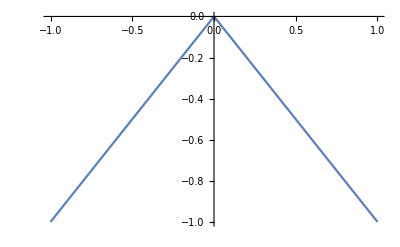

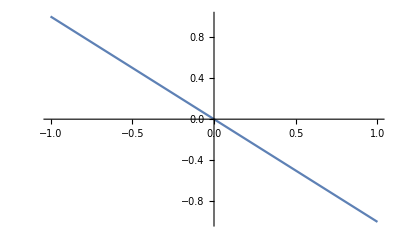

```mathematica
L=1;f[x_]=-x; fpar[x_]:=Piecewise[{{f[-x],-L<x<0},{f[x],0<x<L}}]; fimpar[x_]:=Piecewise[{{-f[-x],-L<x<0},{f[x],0<x<L}}];
Plot[fpar[x],{x,-L,L},ImageSize->Tiny]
Plot[fimpar[x],{x,-L,L},ImageSize->Tiny]
```

```mathematica
a0=1/(2 L) ∫_-L^L fpar[x]ⅆx;
a[n_]:=1/L ∫_-L^L fpar[x] Cos[(n π x)/L]ⅆx;
b[n_]:=1/L ∫_-L^L fpar[x] Sin[(n π x)/L]ⅆx;
t[x_,k_]=a[k] Cos[(k π x)/L]+b[k] Sin[(k π x)/L];
g[x_,q_]:=a0+∑_(k=1)^q t[x,k];
Print["a0=",a0]
Print["an=",a[n]]
Print["bn=",b[n]]
Manipulate[Plot[{fpar[x],g[x,p]},{x,-  L, L},Background->Black,AxesStyle->Red, ImageSize->Small],{p,1,80}]
```

a0=-1/2

an=-(2 (-1+Cos[n π]+n π Sin[n π]))/(n^2 π^2)

bn=0

```mathematica
a0=1/(2 L) ∫_-L^L fimpar[x]ⅆx;
a[n_]:=1/L ∫_-L^L fimpar[x] Cos[(n π x)/L]ⅆx;
b[n_]:=1/L ∫_-L^L fimpar[x] Sin[(n π x)/L]ⅆx;
t[x_,k_]=a[k] Cos[(k π x)/L]+b[k] Sin[(k π x)/L];
g[x_,q_]:=a0+∑_(k=1)^q t[x,k];
Print["a0=",a0]
Print["an=",a[n]]
Print["bn=",b[n]]
Manipulate[Plot[{fimpar[x],g[x,p]},{x,-  L, L},Background->Black,AxesStyle->Red, ImageSize->Small],{p,1,80}]
```

a0=0

an=0

bn=(2 (n π Cos[n π]-Sin[n π]))/(n^2 π^2)

```mathematica
b)   f(x) = cos(2x)
```

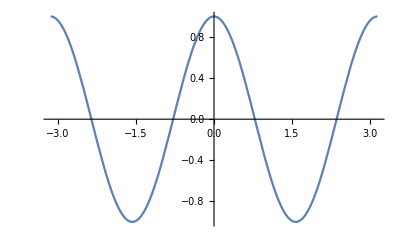

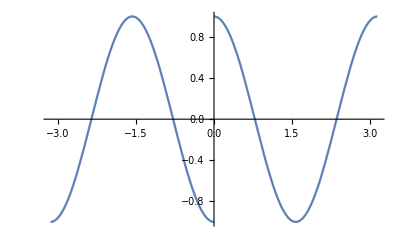

```mathematica
L=Pi;f[x_]=Cos[2 x]; fpar[x_]:=Piecewise[{{f[-x],-L<x<0},{f[x],0<x<L}}]; fimpar[x_]:=Piecewise[{{-f[-x],-L<x<0},{f[x],0<x<L}}];
Plot[fpar[x],{x,-L,L},ImageSize->Tiny]
Plot[fimpar[x],{x,-L,L},ImageSize->Tiny]
```

```mathematica
a0=1/(2 L) ∫_-L^L fpar[x]ⅆx;
a[n_]:=1/L ∫_-L^L fpar[x] Cos[(n π x)/L]ⅆx;
b[n_]:=1/L ∫_-L^L fpar[x] Sin[(n π x)/L]ⅆx;
t[x_,k_]=a[k] Cos[(k π x)/L]+b[k] Sin[(k π x)/L];
g[x_,q_]:=a0+∑_(k=1)^q t[x,k];
Print["a0=",a0]
Print["an=",a[n]]
Print["bn=",b[n]]
Manipulate[Plot[{fpar[x],g[x,p]},{x,-  L, L},Background->Black,AxesStyle->Red, ImageSize->Small],{p,1,80}]
```

a0=0

an=(2 n Sin[n π])/((-4+n^2) π)

bn=0